```mathematica
ψ[p_, q_, v_, c_, r_, z_]:=c[[1]] + c[[2]] r^2+r BesselJ[1,p r ](c[[3]]+ c[[4]]z)+c[[5]] Cos[p z]+c[[6]]Sin[p z]+r^2(c[[7]] Cos[p z]+c[[8]] Sin[p z]) + c[[9]] Cos[p √(r^2+z^2)]+c[[10]] Sin[p √(r^2+z^2)]+r BesselJ[1, v r](c[[11]]Cos[q z]+c[[12]]Sin[q z])+r BesselJ[1, q r](c[[13]]Cos[v z]+ c[[14]]Sin[v z]) + r BesselY[1 ,v r](c[[15]]Cos[q z]+c[[16]]Sin[q z])+ r BesselY[1, q r](c[[17]]Cos[v z]+c[[18]] Sin[v z])
```

```mathematica
c = {0.4733,-0.2164,0.0,0.0,0.0,0.0,-0.06830,0.01220,0.1687,0.8635,-1.0682,0.02166,-0.002662,0.1178,1.4008,-0.2656,1.3770,0.2468};
```

```mathematica
T = 15.2329;
p=√T
q = p/2
v = p √(3/4)
```

3.90293

1.95147

3.38004

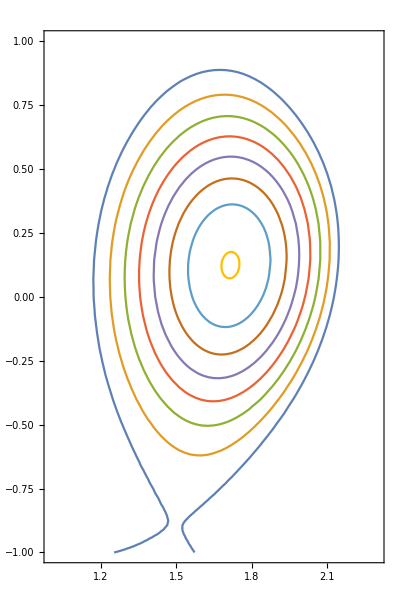

```mathematica
ContourPlot[{0.4733-0.2164 r^2+0.1687 Cos[3.902934793203699 √(r^2+z^2)]+r BesselY[1,3.380040680228568 r] (1.4008 Cos[1.9514673966018494 z]-0.2656 Sin[1.9514673966018494 z])+r BesselJ[1,3.380040680228568 r] (-1.0682 Cos[1.9514673966018494 z]+0.02166 Sin[1.9514673966018494 z])+r BesselJ[1,1.9514673966018494 r] (-0.002662 Cos[3.380040680228568 z]+0.1178 Sin[3.380040680228568 z])+r BesselY[1,1.9514673966018494 r] (1.377 Cos[3.380040680228568 z]+0.2468 Sin[3.380040680228568 z])+r^2 (-0.0683 Cos[3.902934793203699 z]+0.0122 Sin[3.902934793203699 z])+0.8635 Sin[3.902934793203699 √(r^2+z^2)]==0.,0.4733-0.2164 r^2+0.1687 Cos[3.902934793203699 √(r^2+z^2)]+r BesselY[1,3.380040680228568 r] (1.4008 Cos[1.9514673966018494 z]-0.2656 Sin[1.9514673966018494 z])+r BesselJ[1,3.380040680228568 r] (-1.0682 Cos[1.9514673966018494 z]+0.02166 Sin[1.9514673966018494 z])+r BesselJ[1,1.9514673966018494 r] (-0.002662 Cos[3.380040680228568 z]+0.1178 Sin[3.380040680228568 z])+r BesselY[1,1.9514673966018494 r] (1.377 Cos[3.380040680228568 z]+0.2468 Sin[3.380040680228568 z])+r^2 (-0.0683 Cos[3.902934793203699 z]+0.0122 Sin[3.902934793203699 z])+0.8635 Sin[3.902934793203699 √(r^2+z^2)]==0.2,0.4733-0.2164 r^2+0.1687 Cos[3.902934793203699 √(r^2+z^2)]+r BesselY[1,3.380040680228568 r] (1.4008 Cos[1.9514673966018494 z]-0.2656 Sin[1.9514673966018494 z])+r BesselJ[1,3.380040680228568 r] (-1.0682 Cos[1.9514673966018494 z]+0.02166 Sin[1.9514673966018494 z])+r BesselJ[1,1.9514673966018494 r] (-0.002662 Cos[3.380040680228568 z]+0.1178 Sin[3.380040680228568 z])+r BesselY[1,1.9514673966018494 r] (1.377 Cos[3.380040680228568 z]+0.2468 Sin[3.380040680228568 z])+r^2 (-0.0683 Cos[3.902934793203699 z]+0.0122 Sin[3.902934793203699 z])+0.8635 Sin[3.902934793203699 √(r^2+z^2)]==0.4,0.4733-0.2164 r^2+0.1687 Cos[3.902934793203699 √(r^2+z^2)]+r BesselY[1,3.380040680228568 r] (1.4008 Cos[1.9514673966018494 z]-0.2656 Sin[1.9514673966018494 z])+r BesselJ[1,3.380040680228568 r] (-1.0682 Cos[1.9514673966018494 z]+0.02166 Sin[1.9514673966018494 z])+r BesselJ[1,1.9514673966018494 r] (-0.002662 Cos[3.380040680228568 z]+0.1178 Sin[3.380040680228568 z])+r BesselY[1,1.9514673966018494 r] (1.377 Cos[3.380040680228568 z]+0.2468 Sin[3.380040680228568 z])+r^2 (-0.0683 Cos[3.902934793203699 z]+0.0122 Sin[3.902934793203699 z])+0.8635 Sin[3.902934793203699 √(r^2+z^2)]==0.6000000000000001,0.4733-0.2164 r^2+0.1687 Cos[3.902934793203699 √(r^2+z^2)]+r BesselY[1,3.380040680228568 r] (1.4008 Cos[1.9514673966018494 z]-0.2656 Sin[1.9514673966018494 z])+r BesselJ[1,3.380040680228568 r] (-1.0682 Cos[1.9514673966018494 z]+0.02166 Sin[1.9514673966018494 z])+r BesselJ[1,1.9514673966018494 r] (-0.002662 Cos[3.380040680228568 z]+0.1178 Sin[3.380040680228568 z])+r BesselY[1,1.9514673966018494 r] (1.377 Cos[3.380040680228568 z]+0.2468 Sin[3.380040680228568 z])+r^2 (-0.0683 Cos[3.902934793203699 z]+0.0122 Sin[3.902934793203699 z])+0.8635 Sin[3.902934793203699 √(r^2+z^2)]==0.8,0.4733-0.2164 r^2+0.1687 Cos[3.902934793203699 √(r^2+z^2)]+r BesselY[1,3.380040680228568 r] (1.4008 Cos[1.9514673966018494 z]-0.2656 Sin[1.9514673966018494 z])+r BesselJ[1,3.380040680228568 r] (-1.0682 Cos[1.9514673966018494 z]+0.02166 Sin[1.9514673966018494 z])+r BesselJ[1,1.9514673966018494 r] (-0.002662 Cos[3.380040680228568 z]+0.1178 Sin[3.380040680228568 z])+r BesselY[1,1.9514673966018494 r] (1.377 Cos[3.380040680228568 z]+0.2468 Sin[3.380040680228568 z])+r^2 (-0.0683 Cos[3.902934793203699 z]+0.0122 Sin[3.902934793203699 z])+0.8635 Sin[3.902934793203699 √(r^2+z^2)]==1.,0.4733-0.2164 r^2+0.1687 Cos[3.902934793203699 √(r^2+z^2)]+r BesselY[1,3.380040680228568 r] (1.4008 Cos[1.9514673966018494 z]-0.2656 Sin[1.9514673966018494 z])+r BesselJ[1,3.380040680228568 r] (-1.0682 Cos[1.9514673966018494 z]+0.02166 Sin[1.9514673966018494 z])+r BesselJ[1,1.9514673966018494 r] (-0.002662 Cos[3.380040680228568 z]+0.1178 Sin[3.380040680228568 z])+r BesselY[1,1.9514673966018494 r] (1.377 Cos[3.380040680228568 z]+0.2468 Sin[3.380040680228568 z])+r^2 (-0.0683 Cos[3.902934793203699 z]+0.0122 Sin[3.902934793203699 z])+0.8635 Sin[3.902934793203699 √(r^2+z^2)]==1.2000000000000002,0.4733-0.2164 r^2+0.1687 Cos[3.902934793203699 √(r^2+z^2)]+r BesselY[1,3.380040680228568 r] (1.4008 Cos[1.9514673966018494 z]-0.2656 Sin[1.9514673966018494 z])+r BesselJ[1,3.380040680228568 r] (-1.0682 Cos[1.9514673966018494 z]+0.02166 Sin[1.9514673966018494 z])+r BesselJ[1,1.9514673966018494 r] (-0.002662 Cos[3.380040680228568 z]+0.1178 Sin[3.380040680228568 z])+r BesselY[1,1.9514673966018494 r] (1.377 Cos[3.380040680228568 z]+0.2468 Sin[3.380040680228568 z])+r^2 (-0.0683 Cos[3.902934793203699 z]+0.0122 Sin[3.902934793203699 z])+0.8635 Sin[3.902934793203699 √(r^2+z^2)]==1.4000000000000001}, {r, 1, 2.3}, {z, -1, 1}, AspectRatio->2/1.3]
```